```mathematica
ClearSystemCache[]
Clear["Global`*"]
Off[General::spell1] 
Needs["ErrorBarPlots`"]
```

## Load and arrange data:

define folder on pc that contains raw data in .mpa (2D=128x128) format, build a list (called "rawData") of file names with certain names that you have to specify (belonging to one rocking curve)

specify the folder and the file names:

```mathematica
dataFolder=SetDirectory["/media/data/experiments/ILL_VCN_2013/data/Untitled Folder/20130312"]; 
files={"pos*.mpa"};
rawData=FileNames[files]
```

{posScan2_001.mpa,posScan2_002.mpa,posScan2_003.mpa,posScan2_004.mpa,posScan2_005.mpa,posScan2_006.mpa,posScan2_007.mpa,posScan2_008.mpa,posScan2_009.mpa,posScan2_010.mpa,posScan2_011.mpa,posScan2_012.mpa,posScan2_013.mpa,posScan2_014.mpa,posScan2_015.mpa,posScan2_016.mpa,posScan2_017.mpa,posScan2_018.mpa,posScan2_019.mpa,posScan2_020.mpa,posScan2_021.mpa,posScan2_022.mpa,posScan2_023.mpa,posScan2_024.mpa,posScan2_025.mpa,posScan2_026.mpa,posScan2_027.mpa,posScan2_028.mpa}

define function that changes the extension of files names in the list "rawData" from mpa to dat, the new list is called "rawDataRen"

```mathematica
changeExt[x_]:=StringReplace[x,"mpa"->"dat"]
rawDataRen=changeExt[rawData]
```

{posScan2_001.dat,posScan2_002.dat,posScan2_003.dat,posScan2_004.dat,posScan2_005.dat,posScan2_006.dat,posScan2_007.dat,posScan2_008.dat,posScan2_009.dat,posScan2_010.dat,posScan2_011.dat,posScan2_012.dat,posScan2_013.dat,posScan2_014.dat,posScan2_015.dat,posScan2_016.dat,posScan2_017.dat,posScan2_018.dat,posScan2_019.dat,posScan2_020.dat,posScan2_021.dat,posScan2_022.dat,posScan2_023.dat,posScan2_024.dat,posScan2_025.dat,posScan2_026.dat,posScan2_027.dat,posScan2_028.dat}

number of files in the list to be renamed, loaded, plotted,...

```mathematica
j=Length[rawDataRen]
```

28

define function that "physically" (on your harddisk) renames all files on the list that are in the data folder

```mathematica
renFiles[y_,z_]:=Do[RenameFile[ToFileName[dataFolder,y[[n]]],ToFileName[dataFolder,z[[n]]]],{n,1,j,1}]
```

do it! it works even if there is warnings, that are suppressed here

```mathematica
Quiet[renFiles[rawData,rawDataRen]]
```

load renamed data files on the list

```mathematica
loadFiles[k_]:=Table[Import[ToFileName[dataFolder,k[[n]]]],{n,j}]
data=loadFiles[rawDataRen];
```

re-rename files to establish original state of raw data on hard disk

```mathematica
Quiet[renFiles[rawDataRen,rawData]]
```

restructure loaded data

```mathematica
data=Table[Flatten[data[[n]]],{n,j}];
```

remove header in loadad data

```mathematica
data=Table[Take[data[[n]],-16384],{n,1,j}];
```

check length of jth data set. by now "data" should be a list of j lists of 128x128=16384 numbers.

```mathematica
Length[data[[1]]]
```

16384

generate a list of motor positions in degrees: enter below the starting point, stepwidth:

```mathematica
start=0.2;  
step=0.05; 
end=start+(j-1) step;
pos=Range[start,end,step]
```

{0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55}

## Plot 2D detector images:

define function to form list of j det matrices from above list of j lists

```mathematica
dataMatr[p_]:=Table[Partition[p[[n]],128],{n,j}]
data=dataMatr[data];
```

define function to form list of matrix plots

```mathematica
plotData[q_,k_]:=Table[ArrayPlot[Log[q[[n]]],DataReversed->{True,False},MaxPlotPoints->Infinity,ColorFunction->"DarkRainbow",Frame->False],k]
```

plot them

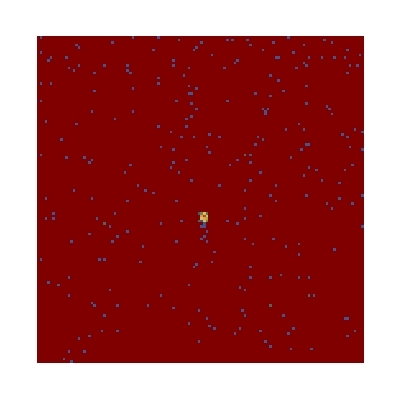
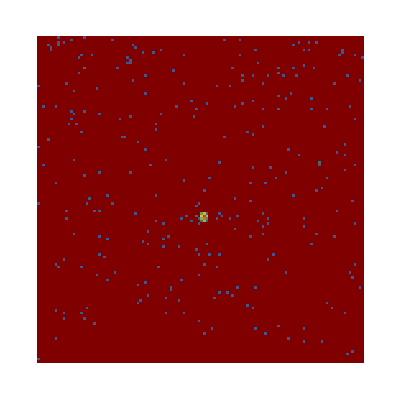
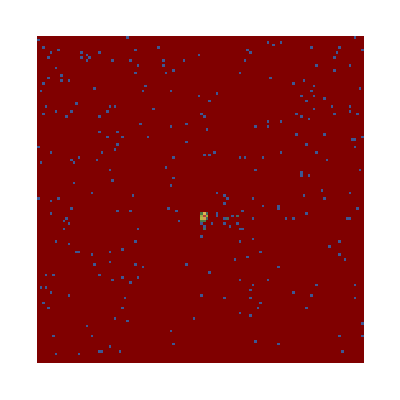
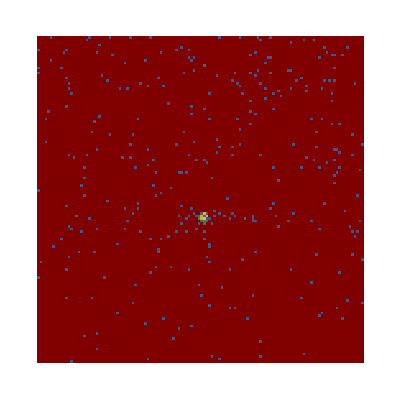
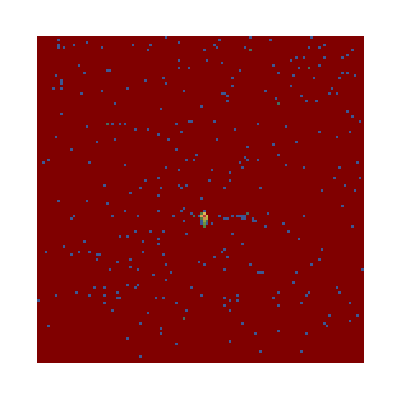
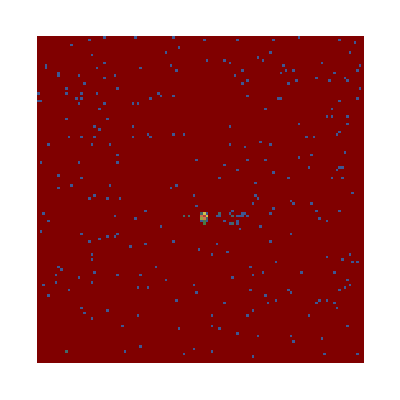
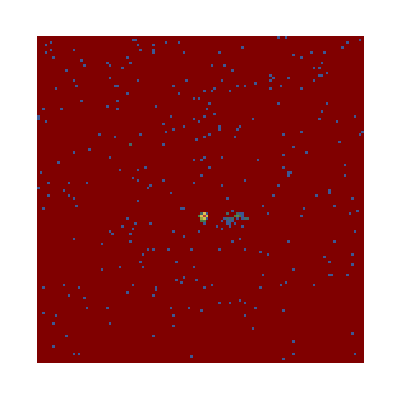
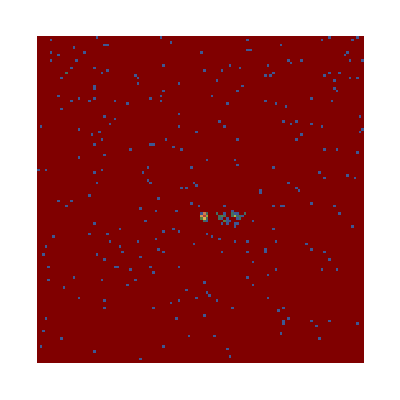

```mathematica
plot=plotData[data,{n,j}]
```

```mathematica
ListPlot3D[data[[12]],PlotRange->{{43,90},{45,61},{0,100}},ColorFunction->"Rainbow",Mesh->None(*,InterpolationOrder->1*)];
```

sum up x measurements to see regions of interest (ROIs)

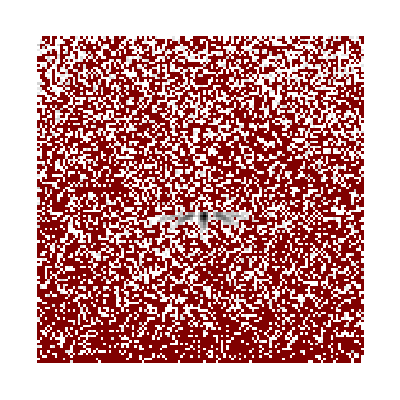

```mathematica
sum=Total[Take[data,{1,j}]]//N;
ArrayPlot[Log[10,sum],DataReversed->{True,False}]
```

```mathematica
ListPlot3D[sum,PlotRange->{Automatic,Automatic,Automatic}];
```

Define ROIs manually by right-clicking on the plot and choosing "Get coordinates". On moving along the plot, you can see the coordinates. 
The first coordinate corresponds to the x-, the second to the y-value. Enter them manually below.
The first and the second number below (the pair in the first list element) denote left and right boundaries, the third and the fourth (the pair in the second list element) lower and upper boundaries, respectively.

```mathematica
roiM2={{50,56},{57,59}};
roiM1={{57,62},{57,59}};
roi0={{63,68},{57,59}};
roiP1={{69,74},{57,59}}; 
roiP2={{75,81},{57,59}};
```

Extract raw data in ROIs,

```mathematica
m2Data=Table[Table[Take[data[[n]][[m]],roiM2[[1]]],{m,roiM2[[2,1]],roiM2[[2,2]]}],{n,j}];
m1Data=Table[Table[Take[data[[n]][[m]],roiM1[[1]]],{m,roiM1[[2,1]],roiM1[[2,2]]}],{n,j}];
zeroData=Table[Table[Take[data[[n]][[m]],roi0[[1]]],{m,roi0[[2,1]],roi0[[2,2]]}],{n,j}];
p1Data=Table[Table[Take[data[[n]][[m]],roiP1[[1]]],{m,roiP1[[2,1]],roiP1[[2,2]]}],{n,j}]; 
p2Data=Table[Table[Take[data[[n]][[m]],roiP2[[1]]],{m,roiP2[[2,1]],roiP2[[2,2]]}],{n,j}];
```

calculate the sum of each ROI data set

```mathematica
m2Sum=Table[Total[m2Data[[n]],2],{n,j}]
m1Sum=Table[Total[m1Data[[n]],2],{n,j}]
zeroSum=Table[Total[zeroData[[n]],2],{n,j}]
p1Sum=Table[Total[p1Data[[n]],2],{n,j}] 
p2Sum=Table[Total[p2Data[[n]],2],{n,j}]
```

{0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,1,1,7,4,9,20,17,19,8,1,4,1}

{0,2,0,3,3,4,0,0,0,4,7,1,7,8,15,17,38,75,85,66,54,32,13,5,3,4,1,1}

{106,109,90,102,86,115,97,80,53,46,24,36,49,88,108,83,68,45,33,26,43,79,91,90,101,108,103,38}

{0,3,3,3,2,4,1,13,41,56,78,63,58,24,15,9,9,4,1,8,2,2,1,4,1,2,4,1}

{0,2,5,3,6,7,24,21,17,11,10,5,1,3,1,1,3,0,0,1,3,0,1,0,0,1,1,1}

## subtract some background:

```mathematica
bckgr=0;
```

```mathematica
m2Sum=m2Sum-bckgr
m1Sum=m1Sum-bckgr
zeroSum=zeroSum-bckgr
p1Sum=p1Sum-bckgr 
p2Sum=p2Sum-bckgr
```

{0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,1,1,7,4,9,20,17,19,8,1,4,1}

{0,2,0,3,3,4,0,0,0,4,7,1,7,8,15,17,38,75,85,66,54,32,13,5,3,4,1,1}

{106,109,90,102,86,115,97,80,53,46,24,36,49,88,108,83,68,45,33,26,43,79,91,90,101,108,103,38}

{0,3,3,3,2,4,1,13,41,56,78,63,58,24,15,9,9,4,1,8,2,2,1,4,1,2,4,1}

{0,2,5,3,6,7,24,21,17,11,10,5,1,3,1,1,3,0,0,1,3,0,1,0,0,1,1,1}

```mathematica
abs[x_]:=If[x<0,0,x] 
m2Sum=Map[abs,m2Sum[[All]],2] 
m1Sum=Map[abs,m1Sum[[All]],2]
zeroSum=Map[abs,zeroSum[[All]],2] 
p1Sum=Map[abs,p1Sum[[All]],2]  
p2Sum=Map[abs,p2Sum[[All]],2]
```

{0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,1,1,7,4,9,20,17,19,8,1,4,1}

{0,2,0,3,3,4,0,0,0,4,7,1,7,8,15,17,38,75,85,66,54,32,13,5,3,4,1,1}

{106,109,90,102,86,115,97,80,53,46,24,36,49,88,108,83,68,45,33,26,43,79,91,90,101,108,103,38}

{0,3,3,3,2,4,1,13,41,56,78,63,58,24,15,9,9,4,1,8,2,2,1,4,1,2,4,1}

{0,2,5,3,6,7,24,21,17,11,10,5,1,3,1,1,3,0,0,1,3,0,1,0,0,1,1,1}

calculate η, its error bar and plot the data

```mathematica
minus2=m2Sum;(*renamed, because error calculation was programmed before...*) 
σMinus2=Table[√minus2[[n]],{n,j}];
minus1=m1Sum;
σMinus1=Table[√minus1[[n]],{n,j}];
zero=zeroSum;
σZero=Table[√zero[[n]],{n,j}];
plus1=p1Sum;
σPlus1=Table[√plus1[[n]],{n,j}]; 
plus2=p2Sum;
σPlus2=Table[√plus2[[n]],{n,j}];


ηMinus2=minus2/(minus1+minus2+plus1+plus2+zero)//N;(*calculate diffraction efficiencies*) 
ηMinus1=minus1/(minus1+minus2+plus1+plus2+zero)//N;
ηZero=zero/(minus1+minus2+plus1+plus2+zero)//N;
ηPlus1=plus1/(minus1+minus2+plus1+plus2+zero)//N; 
ηPlus2=plus2/(minus1+minus2+plus1+plus2+zero)//N;


σηMinus2=√(((minus1+plus1+plus2+zero)^2 σMinus2^2+minus2^2 (σMinus1^2+σPlus1^2+σPlus2^2+σZero^2))/(minus1+minus2+plus1+plus2+zero)^4)//N;(*calculate diffraction efficiency errors*) 
σηMinus1=√(((minus2+plus1+plus2+zero)^2 σMinus1^2+minus1^2 (σMinus2^2+σPlus1^2+σPlus2^2+σZero^2))/(minus1+minus2+plus1+plus2+zero)^4)//N;
σηZero=√((zero^2 (σMinus1^2+σMinus2^2+σPlus1^2+σPlus2^2)+(minus1+minus2+plus1+plus2)^2 σZero^2)/(minus1+minus2+plus1+plus2+zero)^4)//N;
σηPlus1=√(((minus1+minus2+plus2+zero)^2 σPlus1^2+plus1^2 (σMinus1^2+σMinus2^2+σPlus2^2+σZero^2))/(minus1+minus2+plus1+plus2+zero)^4)//N; 
σηPlus2=√(((minus1+minus2+plus1+zero)^2 σPlus2^2+plus2^2 (σMinus1^2+σMinus2^2+σPlus1^2+σZero^2))/(minus1+minus2+plus1+plus2+zero)^4)//N;
```

create lists of harvested data, so that we can plot it:

```mathematica
ηM2=Table[{pos[[n]],ηMinus2[[n]],σηMinus2[[n]]},{n,j}];
ηM1=Table[{pos[[n]],ηMinus1[[n]],σηMinus1[[n]]},{n,j}];
η0=Table[{pos[[n]],ηZero[[n]],σηZero[[n]]},{n,j}];
ηP1=Table[{pos[[n]],ηPlus1[[n]],σηPlus1[[n]]},{n,j}]; 
ηP2=Table[{pos[[n]],ηPlus2[[n]],σηPlus2[[n]]},{n,j}];
```

plot it:

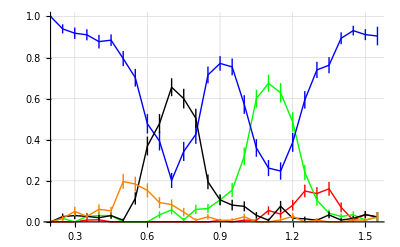

```mathematica
ErrorListPlot[{ηM2,ηM1,η0,ηP1,ηP2},PlotRange->{0,1},PlotStyle->{Red,Green,Blue,Black,Orange},Joined->True,GridLines->Automatic]
```

Form table to be exported for further processing:

```mathematica
allData=Round[Table[{pos[[n]],ηMinus2[[n]],σηMinus2[[n]],ηMinus1[[n]],σηMinus1[[n]],ηZero[[n]],σηZero[[n]],ηPlus1[[n]],σηPlus1[[n]],ηPlus2[[n]],σηPlus2[[n]]},{n,j}],0.00001];
```

Export:

```mathematica
Export[StringReplacePart[files[[1]],".dat",{-5,-1}],allData]
```

pos.dat

```mathematica
"#1A_5.dat"
```

#1A_5.dat